```mathematica
ClearAll["Global`*"]
```

## Model

```mathematica
f1[x_]:=If[Im[w1*x^2+w2*x+w3]==0,w1*x^2+w2*x+w3,10^11];
```

## Data

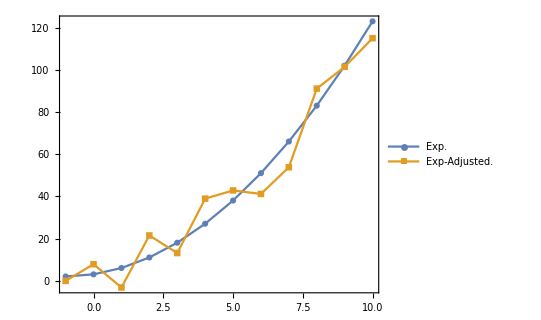

```mathematica
xdata=Table[i,{i,-1,10,1}];
ydata=Map[f1,xdata]/.{w1->1,w2->2,w3->3};
(*ydataAdjusted=Table[ydata[[i]]+RandomReal[{-15,15}],{i,1,Length[ydata]}];*)
ydataAdjusted={-0.10266646127212908,7.812282901372733,-3.2278135465579325,21.443416309796348,13.103181055729578,38.902538519456996,42.7913558921784,41.13754701768447,53.78640767067495,91.0827080115583,101.41853935050891,114.99844409250798};
dataMaker[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}];
expData=dataMaker[xdata,ydata];
expDataAdjusted=dataMaker[xdata,ydataAdjusted];
ListPlot[{expData,expDataAdjusted},Joined->{True, True},PlotMarkers->Automatic,Frame->True,Axes->False,AspectRatio->0.8,PlotLegends->Placed[{"Exp.","Exp-Adjusted."},{0.2,0.8}]]
```

## Non-Linear Model Fit

```mathematica
nlm=NonlinearModelFit[expDataAdjusted,f1[x],{w1,w2,w3},x];
params=nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
w1 | 0.855824 | 0.245918 | 3.48012 | 0.0069373
w2 | 2.8516 | 2.3373 | 1.22004 | 0.253453
w3 | 3.23428 | 4.7282 | 0.684041 | 0.511176

## Parameters

```mathematica
unpack[pars_]:=Table[params[[1,1,i]][[2]],{i,2,4,1}];
pset=unpack[params];
```

## Fitting data

```mathematica
thData=Map[f1,xdata]/.{w1->pset[[1]],w2->pset[[2]],w3->pset[[3]]};
cFit=combodata[xdata,ydataFit];
```

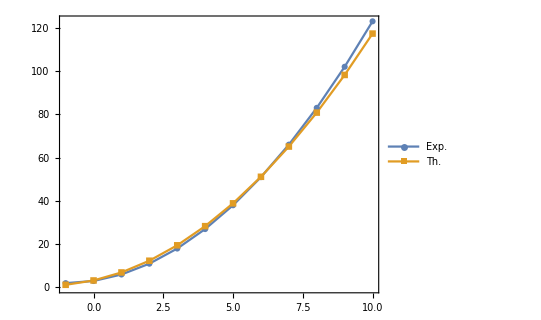

```mathematica
ListPlot[{c1,cFit},Joined->{True, True},PlotMarkers->Automatic,Frame->True,Axes->False,AspectRatio->0.8,PlotLegends->Placed[{"Exp.","Th."},{0.2,0.8}]]
```